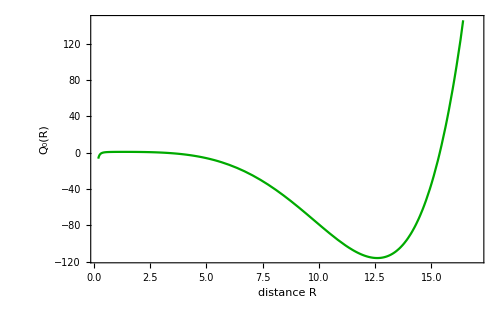

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; msr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0.1;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0a=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2a=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4a=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f2=Plot[q0a,{x,0.2,17},Frame->True,FrameLabel->{"distance R"," Q_0(R)"},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

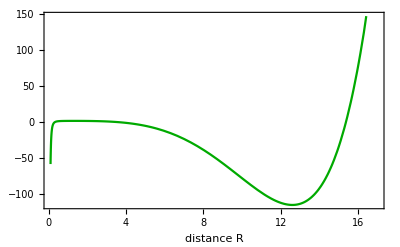

```mathematica
f20=Plot[q0a,{x,0.1,17},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

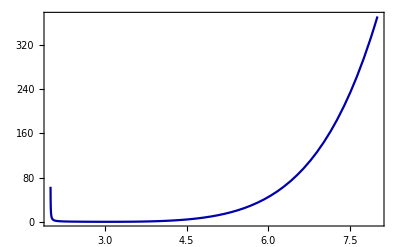

```mathematica
f2a=Plot[q2a,{x,2.003,8},Frame->True,PlotStyle->{Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

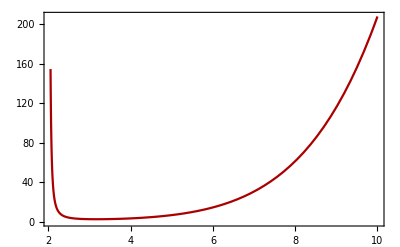

```mathematica
f2b=Plot[q4a,{x,2.05,10},Frame->True,PlotStyle->{Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

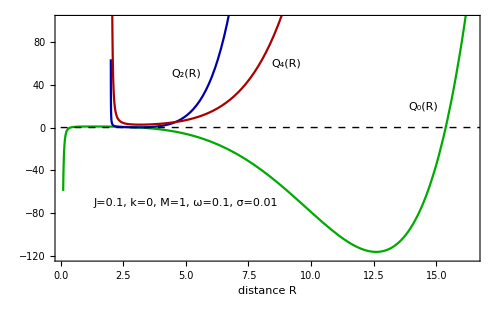

```mathematica
fig1a=Show[f20,f2a,f2b, Graphics[{Inset[Framed["J=0.1, k=0, M=1, ω=0.1, σ=0.01"],{5,-70},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{5,50},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{14.5,20},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{9,60},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{17,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-120,100}]
```

```mathematica
Export["C:\\Users\\Giannis\\OneDrive - ΠΑΝΕΠΙΣΤΗΜΙΟ ΙΩΑΝΝΙΝΩΝ\\Έγγραφα\\COHENfig10.eps",fig1a,"EPS"]
```

C:\Users\Giannis\OneDrive - ΠΑΝΕΠΙΣΤΗΜΙΟ ΙΩΑΝΝΙΝΩΝ\Έγγραφα\COHENfig10.eps